# Álgebra

## Expressões algébricas

Fatorar expressões algébricas:

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

Expandir expressões algébricas:

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

## Igualdades

Testar igualdades:

```mathematica
2+2==4
```

True

Combinar expressões algébricas para representar uma equação:

```mathematica
1+z==15
```

1+z==15

## Desigualdades

Reduza um conjunto de desigualdades a uma forma simples:

```mathematica
Reduce[{0 < x < 2, 1 ≤ x ≤ 4}, x]
```

1≤x<2

A forma reduzida pode incluir múltiplos intervalos:

```mathematica
Reduce[(x - 1) (x - 2) (x - 3) (x - 4) > 0, x]
```

x<1||2<x<3||x>4

Visualizar intervalos como segmentos de reta:

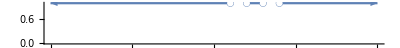

```mathematica
NumberLinePlot[x < 1 || 2 < x < 3 || x > 4, {x, -10, 10}]
```

## Solução de Equações polinomiais

Encontram soluções exatas para equações:

```mathematica
Solve[x^2 + 5 x - 6 == 0, x]
```

{{x→-6},{x→1}}

Encontram soluções numéricas para equações:

```mathematica
NSolve[7 x^2 + 3 x - 5 == 0, x]
```

{{x→-1.08618},{x→0.657611}}

Sistema de equações são listas:

```mathematica
Solve[{x^2 + 5 == y, 7 x - 5 == y}, {x, y}]
```

{{x→2,y→9},{x→5,y→30}}

Encontre as raízes de uma equação:

```mathematica
Roots[x^2 + 3 x - 4 == 0, x]
```

x==-4||x==1

Encontre as raízes calculadas de forma numérica:

```mathematica
NRoots[360 + 234 x - 1051 x^2 + 11 x^3 + 304 x^4 - 20 x^5 == 0, x]
```

x==-1.79025||x==-0.498678||x==0.797819||x==1.68398||x==15.0071

## Exemplo de Manipulação de Equações

```mathematica
equacaoQuadratica = (a*x^2+b*x+c==0);
exemplo1 = {a->1, b->3,c->-10};
exemplo2 = {a->1, b->2,c->-3};
```

```mathematica
solucaoGeral = Solve[equacaoQuadratica,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
solucaoGeral/.exemplo1
```

{{x→-5},{x→2}}

```mathematica
solucaoGeral/.exemplo2
```

{{x→-3},{x→1}}